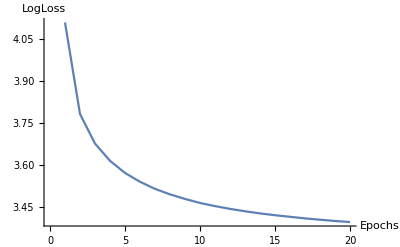

```mathematica
ListPlot[{4.1110142286154,3.783095230168,3.6770896408898,3.6153165629948,3.5719062106418,3.5401830584545,3.514767712588,3.4951914667371,3.4787777099075,3.46430630786,3.4530487264475,3.4431234709839,3.4345128427297,3.4269757588545,3.4204364553734,3.414736302633,3.4090338346992,3.404332674805,3.3997620245825,3.3960777861387},Joined->True,AxesLabel->{"Epochs","LogLoss"}]
```

```mathematica
training={47.299701979287,41.179284409564,37.766593978614,35.292734575989,34.494907763858,33.916951834473,32.223131292312,31.785634513463,31.41358650826,31.12707021014,31.216498415689,30.002964795208,30.045003518891,29.583658460973,29.114315438908,28.884481119283,29.158941561061,29.4344193607,29.217634358033,28.682867813138,28.6088196323}
valid={49.69408856123,43.789203168348,40.367110993395,38.98498919118,37.963217871248,37.902071897477,36.55287646736,36.083600944467,35.993975560697,36.053113513674,36.419600763947,35.175485270538,35.65738649886,35.419057890764,35.354077653732,35.023237092479,34.92936235871,35.156525299582,34.909269542213,35.001403929018}
```

{47.2997,41.1793,37.7666,35.2927,34.4949,33.917,32.2231,31.7856,31.4136,31.1271,31.2165,30.003,30.045,29.5837,29.1143,28.8845,29.1589,29.4344,29.2176,28.6829,28.6088}

{49.6941,43.7892,40.3671,38.985,37.9632,37.9021,36.5529,36.0836,35.994,36.0531,36.4196,35.1755,35.6574,35.4191,35.3541,35.0232,34.9294,35.1565,34.9093,35.0014}

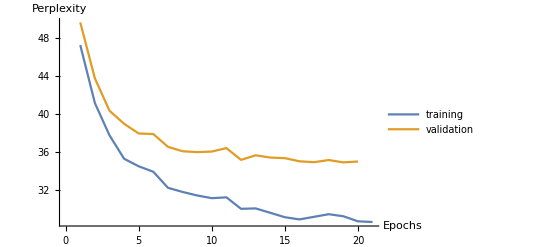

```mathematica
ListPlot[{training,valid},Joined->True,AxesLabel->{"Epochs","Perplexity"},PlotLegends->{"training","validation"}]
```

{0.340007,1972.96,4146.06,6068.89,7670.41,9264.02,10570.5,11845.7,13118.5,14392.9,15667.8}

{1.01686,648.908,1210.28,1764.48,2317.13,2868.35,3421.19,3972.87,4523.99,5075.89,5627.19,6204.31,6791.87,7406.37,8038.2,8669.89,9336.53,9977.06,10627.,11282.,11954.3,12610.,13264.3,13904.8,14549.9,15202.8}

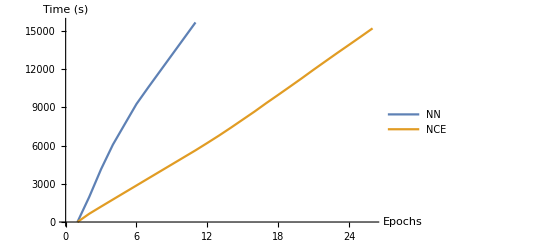

```mathematica
time1={0.340007,1972.960729,4146.064104,6068.886786,7670.408403,9264.019387,10570.450595,11845.6814,13118.480352,14392.864943,15667.840405}
time2={1.016862,648.907839,1210.283053,1764.477531,2317.129896,2868.351556,3421.191054,3972.868033,4523.99493,5075.892122,5627.191652,6204.312967,6791.868471,7406.374799,8038.204507,8669.889009,9336.529328,9977.061593,10626.978516,11282.036048,11954.256439,12610.011233,13264.258413,13904.802807,14549.938194,15202.81923}
ListPlot[{time1,time2},Joined->True,AxesLabel->{"Epochs","Time (s)"},PlotLegends->{"NN","NCE"}]
```

{8.00209,3.87684,3.67779,3.54559,3.4448,3.36798,3.30225,3.24753,3.20046,3.15975,3.12263,3.0902,3.05869,3.03267,3.00847,2.98679,2.96608,2.94798,2.93078,2.91409,2.90073}

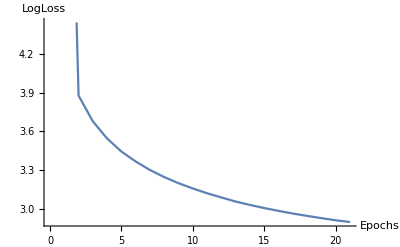

```mathematica
list={8.0020912630873,3.8768386127593,3.6777921836448,3.5455920167494,3.4448045738013,3.367984651611,3.3022470451279,3.2475326251567,3.2004648969847,3.1597451825345,3.1226270307284,3.0901990602353,3.0586857077619,3.032670014797,3.008469303226,2.9867850853402,2.9660801744208,2.9479811369658,2.9307783907003,2.9140854749776,2.9007321260614}
ListPlot[{list},Joined->True,AxesLabel->{"Epochs","LogLoss"}]
```